```mathematica
VertexList[MobiusGraph5[K5Key,allGraphs5]]
```

{n12x34x5,n12x35x4,n12x3x45,n13x24x5,n13x25x4,n13x2x45,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x23x45,n1x24x35,n1x25x34,n1x2x3x4x5,n12345,n1234x5,n1235x4,n123x45,n123x4x5,n1245x3,n124x35,n124x3x5,n125x34,n125x3x4,n12x345,n12x3x4x5,n1345x2,n134x25,n134x2x5,n135x24,n135x2x4,n13x245,n13x2x4x5,n145x23,n145x2x3,n14x235,n14x2x3x5,n15x234,n15x2x3x4,n1x2345,n1x234x5,n1x235x4,n1x23x4x5,n1x245x3,n1x24x3x5,n1x25x3x4,n1x2x345,n1x2x34x5,n1x2x35x4,n1x2x3x45}

```mathematica
ColorSchemeForLists[l1_,l2_]:=Block[{
int = Intersection[l1,l2]},
Join[
Table[e->Darker[Green],{e,SetDifference[l1,int]}],
Table[e->Blue,{e,SetDifference[l2,int]}],
Table[e->Red,{e,int}]
]
]
```

```mathematica
ShowMe[key_]:=With[{
first=Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs5[key,"colofour"]]],
second=Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs5[key,"colofourrealnull"]]],
all=MobiusGraph5[K5Key,allGraphs5]
},
Labeled[
Graph[all,VertexStyle->ColorSchemeForLists[first,second],ImageSize->1200],
s]
]
```

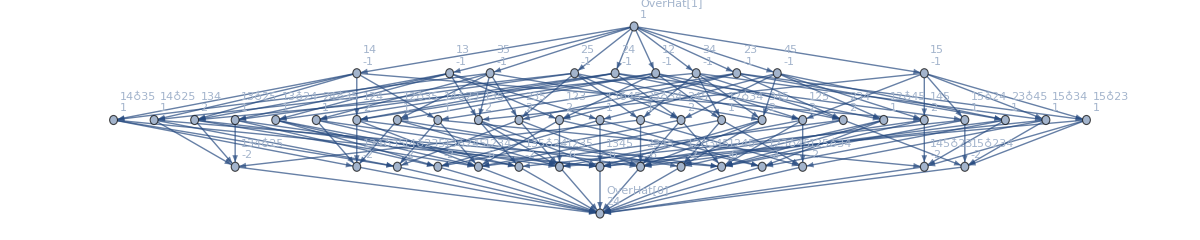
-Graphics-s

```mathematica
ShowMe[1]
```

```mathematica
ShowMe[10]
```

-Graphics-s

```mathematica
ShowMe[1]
```

-Graphics-s

```mathematica
ShowMe[K4Key]
```

-Graphics-s